Mixed Chinese Postman Problem MCPP implementation in Mathematica
by Peter Burbery

The Mixed Chinese Postman Problem is finding the minimum cost traversal of a mixed graph that covers each edge at least once. The problem is NP hard which was proved in 1976. My goal is to program a function that computes the MCPP optimum tour for a mixed graph in Mathematica.
I constructed a mixed graph paclet and submitted, updated, and documented the functions to the Paclet Repository.

## Mixed Graph Paclet

Load the package and context:

```mathematica
PacletInstall["PeterBurbery/MixedGraphs"]
```

PacletObject[…]

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

Generate random mixed graphs

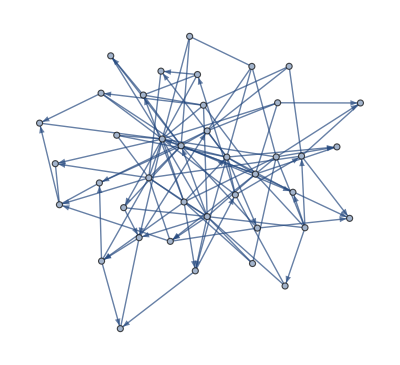

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[40,3],0.68]
```

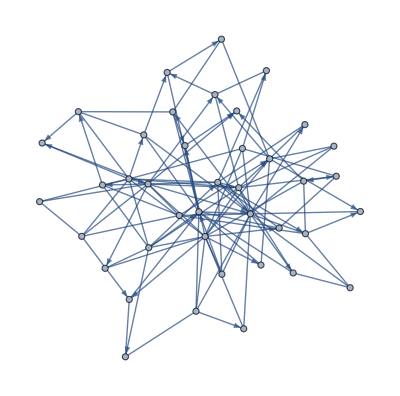

```mathematica
RandomWeightedMixedGraph[BarabasiAlbertGraphDistribution[40,3],0.68,RandomInteger[{1,7}]&]
```

### subsection (if needed)

text

```mathematica
image output
```

## Section 2

combination of text, input and output cells

item 1

item 2

subitem

```mathematica
code and output
```

You can change the style of the cell by highlighting it then use the tap Format -> Style , then choose the needed style

and so on...

Don’t forget to add a lead image at the beginning of the post if you have one